```mathematica
level[t_]:=4.161*10^-6 t^3- .002507 t^2+.9097t-24.32
```

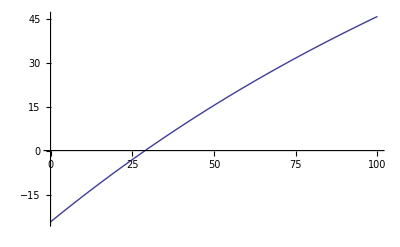

```mathematica
Plot[level[t], {t,0,100}]
```

```mathematica
Reduce[y==4.161*10^-6 t^3- .002507 t^2+.9097t-24.32 ,t]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

t==Root[-1.46456×10^26-6.02202×10^24 y+5.47824×10^24 #1-1.50972×10^22 #1^2+2.50576×10^19 #1^3&,1]||t==Root[-1.46456×10^26-6.02202×10^24 y+5.47824×10^24 #1-1.50972×10^22 #1^2+2.50576×10^19 #1^3&,2]||t==Root[-1.46456×10^26-6.02202×10^24 y+5.47824×10^24 #1-1.50972×10^22 #1^2+2.50576×10^19 #1^3&,3]

```mathematica
ToRadicals[%]
```

t==200.833+(1.54102×10^24-2.66912×10^24 ⅈ)/(-9.28684×10^66+1.02091×10^65 y+1.02091×10^65 √(10661.4-181.933 y+1. y^2))^(1/3)-(5.27916×10^-21+9.14378×10^-21 ⅈ) (-9.28684×10^66+1.02091×10^65 y+1.02091×10^65 √(10661.4-181.933 y+1. y^2))^(1/3)||t==200.833+(1.54102×10^24+2.66912×10^24 ⅈ)/(-9.28684×10^66+1.02091×10^65 y+1.02091×10^65 √(10661.4-181.933 y+1. y^2))^(1/3)-(5.27916×10^-21-9.14378×10^-21 ⅈ) (-9.28684×10^66+1.02091×10^65 y+1.02091×10^65 √(10661.4-181.933 y+1. y^2))^(1/3)||t==200.833-3.08204×10^24/(-9.28684×10^66+1.02091×10^65 y+1.02091×10^65 √(10661.4-181.933 y+1. y^2))^(1/3)+1.05583×10^-20 (-9.28684×10^66+1.02091×10^65 y+1.02091×10^65 √(10661.4-181.933 y+1. y^2))^(1/3)

```mathematica
inv[y_]:=200.83313306096292-3.082037376623253*^24/(-9.286839548678612*^66+1.0209084271727317*^65 y+1.0209084271727317*^65 √(10661.354043359404-181.93286099904697 y+1. y^2))^(1/3)+1.0558328416631367*^-20 (-9.286839548678612*^66+1.0209084271727317*^65 y+1.0209084271727317*^65 √(10661.354043359404-181.93286099904697 y+1. y^2))^(1/3)
```

```mathematica
Clear["Globals`*"]
```

```mathematica
level[5]
```

-19.8337

```mathematica
inv[-19.8337]
```

4.99995

```mathematica
FullSimplify[inv[y], y<100]
```

200.833-3.08204×10^24/(-9.28684×10^66+1.02091×10^65 y+1.02091×10^65 √(10661.4+y (-181.933+1. y)))^(1/3)+1.05583×10^-20 (-9.28684×10^66+1.02091×10^65 y+1.02091×10^65 √(10661.4+y (-181.933+1. y)))^(1/3)

```mathematica
CForm[inv[level]]
```

200.83313306096292 - 3.082037376623253e24/
    Power(-9.286839548678612e66 + 1.0209084271727317e65*level + 
      1.0209084271727317e65*Sqrt(10661.354043359404 - 
         181.93286099904697*level + 1.*Power(level,2)),
     0.3333333333333333) + 1.0558328416631367e-20*
    Power(-9.286839548678612e66 + 1.0209084271727317e65*level + 
      1.0209084271727317e65*Sqrt(10661.354043359404 - 
         181.93286099904697*level + 1.*Power(level,2)),
     0.3333333333333333)